# Homework assignment 5

Kyle McGraw <kmcgraw@caltech.edu>, Collaborated with Dallas Taylor, Allison Glynn

## Part 1: Improving Boolean logic circuit modules.

Here you will choose one of the two-input gates demonstrated in the DigitalCircuitCRNs.nb notebook (AND, OR, XOR, XNOR) and make it better, or at least different.

```mathematica
SetDirectory[NotebookDirectory[]];
Get["CRNSimulator.m"]
Get["CRNSimulatorExtensions.m"]
```

```mathematica
CRNrestore[X_,Y_]:={rxn[2X,2X+Y,1],rxn[2X+Y,2X,2],rxn[Y,0,1],rxn[X+Y,X+2Y,2]}
frestore[x_]:=x^2/(1-2x+2x^2)
```

XOR

Exclusive-or requires that an “ON” output is generated if and only if exactly one input is “ON”.  If “ON” was represented by +1 and “OFF” by -1, then the output should be minus the product of the inputs, i.e. z = -x y for perfect inputs.  But here we represent “ON” by 1 and “OFF” by 0, so the formula for XOR converts to ±1  and back again.  It simplifies to the difference of a sum and a product.  Again, the rectification aspect of the rectified subtraction never comes into play, because the formula will always be non-negative for non-negative inputs.

```mathematica
Simplify[1-((2x-1)(2y-1)+1)/2]
```

x+y-2 x y

```mathematica
CRNxor[X_,Y_,Z_]:=Module[{S,T},{rxn[X,X+T,1],rxn[Y,Y+T,1],rxn[T,0,1],rxn[X+Y,X+Y+S,2],rxn[T+S,0,1000]}~Join~CRNrestore[T,Z]]
fxor[x_,y_]:=frestore[1-((2x-1)(2y-1)+1)/2]
```

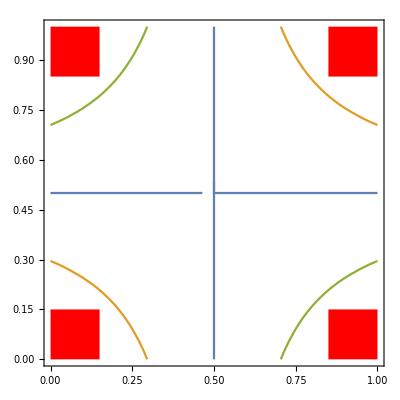

```mathematica
With[{ϵ=0.15},Show[
ContourPlot[{fxor[x,y]==0.5,fxor[x, y]==ϵ,fxor[x, y]==1-ϵ},{x,0,1},{y,0,1}],
Graphics[{Red,Rectangle[{1-ϵ,1-ϵ},{1,1}],Rectangle[{0,0},{ϵ,ϵ}],Rectangle[{1-ϵ,0},{1,ϵ}],Rectangle[{0,1-ϵ},{ϵ,1}]}]
]]
```

```mathematica
CRNxor[X,Y,Z]
```

{  X⟶^1T$2643+X,  Y⟶^1T$2643+Y,  T$2643⟶^10,  X+Y⟶^2S$2643+X+Y,  S$2643+T$2643⟶^10000,  2 T$2643⟶^12 T$2643+Z,  2 T$2643+Z⟶^22 T$2643,  Z⟶^10,  T$2643+Z⟶^2T$2643+2 Z}

```mathematica
Join[{ " "X⟶^1T$14080+X, " "Y⟶^1T$14080+Y, " "T$14080⟶^10, " "X+Y⟶^2S$14080+X+Y, " "S$14080+T$14080⟶^10000},CRNrestore[T$14080,Z]]
```

{  X⟶^1T$14080+X,  Y⟶^1T$14080+Y,  T$14080⟶^10,  X+Y⟶^2S$14080+X+Y,  S$14080+T$14080⟶^10000,  2 T$14080⟶^12 T$14080+Z,  2 T$14080+Z⟶^22 T$14080,  Z⟶^10,  T$14080+Z⟶^2T$14080+2 Z}

```mathematica
tmax=20;
Show[Plot3D[fxor[x,y],{x,0,1},{y,0,1}],
ListPointPlot3D[Flatten[Table[{x0,y0,Z[tmax]}/.SimulateRxnsys[Join[CRNxor[X,Y,Z],{conc[X,x0],conc[Y,y0]}],tmax],{x0,0,1,0.1},{y0,0,1,0.1}],{2}]]]
```

-Graphics3D-

(a) For your chosen gate, determine approximately what is the maximum ϵ  for the basic digital abstraction discussed in class (i.e. any input/output value v in the range 0≤v≤ϵ is interpreted as a valid “False” or “Off” signal, while in the range 1-ϵ≤v≤1  it is interpreted as a valid “True” or “On” signal, and otherwise it is considered invalid) such that all valid inputs give rise to valid outputs.  Analytic derivations are fine, as are empirical calculations to 2 digits of precision. 

From graphing on desmos and mathematicas maximize function, we get the the maximum ϵ  is 0.2282. This matches what we see from empirical calculations with 2 digits of precision, where 0.22 is  the maximum since 0.23 is too large.

```mathematica
Maximize[{x,fxor[x,x]<x, x>0,x<0.49},x]
```

{0.228155,{x→0.228155}}

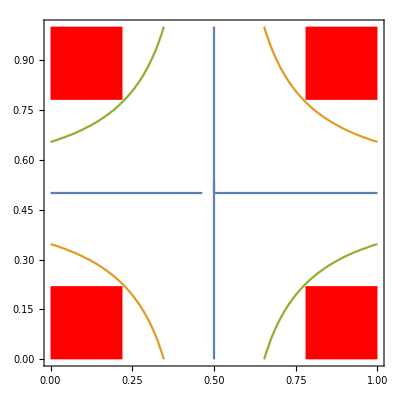

```mathematica
With[{ϵ=0.22},Show[
ContourPlot[{fxor[x,y]==0.5,fxor[x, y]==ϵ,fxor[x, y]==1-ϵ},{x,0,1},{y,0,1}],
Graphics[{Red,Rectangle[{1-ϵ,1-ϵ},{1,1}],Rectangle[{0,0},{ϵ,ϵ}],Rectangle[{1-ϵ,0},{1,ϵ}],Rectangle[{0,1-ϵ},{ϵ,1}]}]
]]
```

```mathematica
maxϵ=0.22;
fxor[maxϵ,maxϵ]
1-fxor[maxϵ,1-maxϵ]
```

0.21448

0.21448

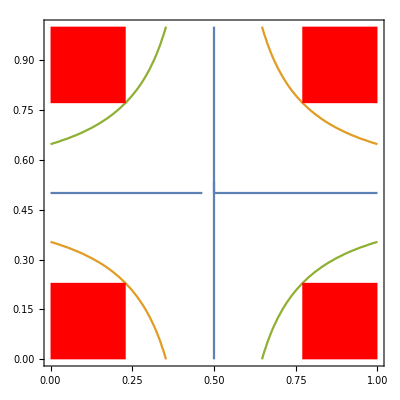

```mathematica
With[{ϵ=0.23},Show[
ContourPlot[{fxor[x,y]==0.5,fxor[x, y]==ϵ,fxor[x, y]==1-ϵ},{x,0,1},{y,0,1}],
Graphics[{Red,Rectangle[{1-ϵ,1-ϵ},{1,1}],Rectangle[{0,0},{ϵ,ϵ}],Rectangle[{1-ϵ,0},{1,ϵ}],Rectangle[{0,1-ϵ},{ϵ,1}]}]
]]
```

```mathematica
overmaxϵ=0.23;
fxor[overmaxϵ,overmaxϵ]
1-fxor[overmaxϵ,1-overmaxϵ]
```

0.231252

0.231252

(b) Design a new CRN module for the same Boolean logic gate that satisfies a digital abstraction with a larger ϵ, say perhaps twice as large.  Your CRN should still have the features that inputs are used catalytically (so their concentrations won’t be changed by the gate), the initial concentrations can be arbitrary, and for any valid inputs, the outputs converge reasonably quickly to a valid and correct value.  It is OK for this CRN module to be larger, in terms of the number of reactions, than the original.  

To satisfy with a larger ϵ, we can add more reactions to restore the signal even further and satisfy a larger ϵ.

```mathematica
Simplify[1-((2x-1)(2y-1)+1)/2]
```

x+y-2 x y

```mathematica
CRNxor[X_,Y_,Z_]:=Module[{S,T,R},{rxn[X,X+T,1],rxn[Y,Y+T,1],rxn[T,0,1],rxn[X+Y,X+Y+S,2],rxn[T+S,0,1000]}~Join~CRNrestore[T,R]~Join~CRNrestore[R,Z]]
fxor[x_,y_]:=frestore[frestore[x+y-2 x y]]
```

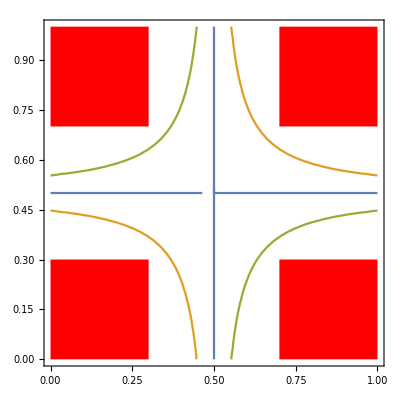

```mathematica
With[{ϵ=0.3},Show[
ContourPlot[{fxor[x,y]==0.5,fxor[x, y]==ϵ,fxor[x, y]==1-ϵ},{x,0,1},{y,0,1}],
Graphics[{Red,Rectangle[{1-ϵ,1-ϵ},{1,1}],Rectangle[{0,0},{ϵ,ϵ}],Rectangle[{1-ϵ,0},{1,ϵ}],Rectangle[{0,1-ϵ},{ϵ,1}]}]
]]
```

```mathematica
Maximize[{x,fxor[x,x]<x, x>0,x<0.49},x]
```

{0.372354,{x→0.372354}}

```mathematica
CRNxor[X,Y,Z]
```

{  X⟶^1T$18946+X,  Y⟶^1T$18946+Y,  T$18946⟶^10,  X+Y⟶^2S$18946+X+Y,  S$18946+T$18946⟶^10000,  2 T$18946⟶^1R$18946+2 T$18946,  R$18946+2 T$18946⟶^22 T$18946,  R$18946⟶^10,  R$18946+T$18946⟶^22 R$18946+T$18946,  2 R$18946⟶^12 R$18946+Z,  2 R$18946+Z⟶^22 R$18946,  Z⟶^10,  R$18946+Z⟶^2R$18946+2 Z}

```mathematica
Join[{ " "X⟶^1T$14080+X, " "Y⟶^1T$14080+Y, " "T$14080⟶^10, " "X+Y⟶^2S$14080+X+Y, " "S$14080+T$14080⟶^10000},CRNrestore[T$14080,R14080],CRNrestore[R14080,Z]]
```

{  X⟶^1T$14080+X,  Y⟶^1T$14080+Y,  T$14080⟶^10,  X+Y⟶^2S$14080+X+Y,  S$14080+T$14080⟶^10000,  2 T$14080⟶^1R14080+2 T$14080,  R14080+2 T$14080⟶^22 T$14080,  R14080⟶^10,  R14080+T$14080⟶^22 R14080+T$14080,  2 R14080⟶^12 R14080+Z,  2 R14080+Z⟶^22 R14080,  Z⟶^10,  R14080+Z⟶^2R14080+2 Z}

```mathematica
tmax=20;
Show[Plot3D[fxor[x,y],{x,0,1},{y,0,1}],
ListPointPlot3D[Flatten[Table[{x0,y0,Z[tmax]}/.SimulateRxnsys[Join[CRNxor[X,Y,Z],{conc[X,x0],conc[Y,y0]}],tmax],{x0,0,1,0.1},{y0,0,1,0.1}],{2}]]]
```

-Graphics3D-

(c)  Design a new CRN module for the same Boolean logic gate that has fewer reactions than the original, but still satisfies a digital abstraction, although perhaps for a smaller value of ϵ. This might not be easy, but be creative!  If you are having trouble with your original choice of gate, it’s OK to choose a different gate (AND, OR, XOR, XNOR) just for this part.  

We can get rid of a reaction (but need a slightly smaller ϵ) by having our XOR just be the absolute value of X-Y. This would give us our intended outputs of 1 only when X or Y is 1.

```mathematica
Simplify[Abs[x-y]]
```

Abs[x-y]

```mathematica
CRNxor[X_,Y_,Z_]:=Module[{T},{rxn[X,X+T,1],rxn[Y,Y+T,1],rxn[T,0,1],rxn[X+Y,0,1000]}~Join~CRNrestore[T,Z]]
fxor[x_,y_]:=frestore[Abs[x-y]]
```

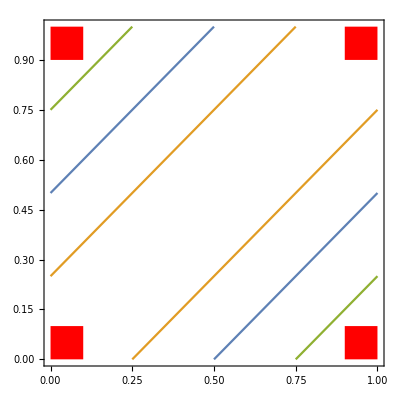

```mathematica
With[{ϵ=0.1},Show[
ContourPlot[{fxor[x,y]==0.5,fxor[x, y]==ϵ,fxor[x, y]==1-ϵ},{x,0,1},{y,0,1}],
Graphics[{Red,Rectangle[{1-ϵ,1-ϵ},{1,1}],Rectangle[{0,0},{ϵ,ϵ}],Rectangle[{1-ϵ,0},{1,ϵ}],Rectangle[{0,1-ϵ},{ϵ,1}]}]
]]
```

```mathematica
Maximize[{x,fxor[x,x]<x, x>0,x<0.49},x]
```

{0.49,{x→0.49}}

```mathematica
overmaxϵ=0.23;
fxor[overmaxϵ,overmaxϵ]
1-fxor[overmaxϵ,1-overmaxϵ]
```

0.

0.420509

```mathematica
CRNxor[X,Y,Z]
```

{  X⟶^1T$24615+X,  Y⟶^1T$24615+Y,  T$24615⟶^10,  X+Y⟶^10000,  2 T$24615⟶^12 T$24615+Z,  2 T$24615+Z⟶^22 T$24615,  Z⟶^10,  T$24615+Z⟶^2T$24615+2 Z}

```mathematica
Join[{ " "X⟶^1T$14080+X, " "Y⟶^1T$14080+Y, " "T$14080⟶^10, " "X+Y⟶^2S$14080+X+Y, " "S$14080+T$14080⟶^10000},CRNrestore[T$14080,R],CRNrestore[R,Z]]
```

{  X⟶^1T$14080+X,  Y⟶^1T$14080+Y,  T$14080⟶^10,  X+Y⟶^2S$14080+X+Y,  S$14080+T$14080⟶^10000,  2 T$14080⟶^1R+2 T$14080,  R+2 T$14080⟶^22 T$14080,  R⟶^10,  R+T$14080⟶^22 R+T$14080,  2 R⟶^12 R+Z,  2 R+Z⟶^22 R,  Z⟶^10,  R+Z⟶^2R+2 Z}

```mathematica
tmax=20;
Show[Plot3D[fxor[x,y],{x,0,1},{y,0,1}],
ListPointPlot3D[Flatten[Table[{x0,y0,Z[tmax]}/.SimulateRxnsys[Join[CRNxor[X,Y,Z],{conc[X,x0],conc[Y,y0]}],tmax],{x0,0,1,0.1},{y0,0,1,0.1}],{2}]]]
```

-Graphics3D-

(d) Choose a circuit with at least 10 gates that uses the gate of your choice at least a few times.  You may do the following with either the original CRN module examined in part (a) or your inventions from (b) or (c), using the original modules for the gates you didn’t design.  Provide code that exhaustive tests every possible Boolean input case, where the “worst-case” concentrations (ϵ or 1-ϵ) are used,  and verifies that the CRN calculates correctly with respect to the digital abstraction. Roughly what is the largest ϵ such that the output of your circuit is valid for any Boolean input case?  This value of ϵ might be larger than, but will not be smaller than, the value of ϵ  for which the individual gate modules are guaranteed.  Explain why.  If your chosen circuit does not demonstrate this property, that the circuit as a whole can tolerate more substantial input imperfection than any individual logic gate can, invent a circuit for which it’s true.

```mathematica
CRNand[X_,Y_,Z_]:=Module[{W},{rxn[X+Y,X+Y+W,1],rxn[W,0,1]}~Join~CRNrestore[W,Z]]
CRNor[X_,Y_,Z_]:=Module[{W},{rxn[X,X+W,0.85],rxn[Y,Y+W,.85],rxn[W,0,1]}~Join~CRNrestore[W,Z]]
CRNxor[X_,Y_,Z_]:=Module[{S,T},{rxn[X,X+T,1],rxn[Y,Y+T,1],rxn[T,0,1],rxn[X+Y,X+Y+S,2],rxn[T+S,0,1000]}~Join~CRNrestore[T,Z]]
```

```mathematica
CRNhalfadder[X1_,X2_,Z1_,Z2_]:=CRNxor[X1,X2,Z1]~Join~CRNand[X1,X2,Z2]
CRNfulladder[X1_,X2_,X3_,Z1_,Z2_]:=Module[{Y1,Y2,Y3},CRNhalfadder[X1,X2,Y1,Y2]~Join~CRNhalfadder[X3,Y1,Z1,Y3]~Join~CRNor[Y3,Y2,Z2]]
CRN3bitadder[X1_,X2_,X3_,Y1_,Y2_,Y3_,Z1_,Z2_,Z3_,Z4_]:=Module[{A1,A2},CRNhalfadder[X1,Y1,Z1,A1]~Join~CRNfulladder[X2,Y2,A1,Z2,A2]~Join~CRNfulladder[X3,Y3,A2,Z3,Z4]]
```

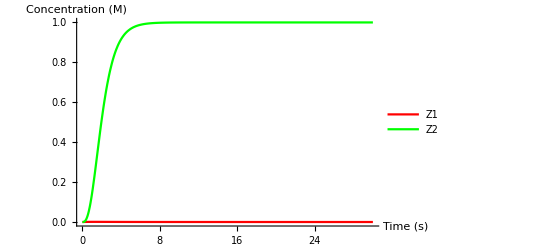

```mathematica
tmax=30;
rsys=CRNhalfadder[X1,X2,Z1,Z2];
sol=SimulateRxnsys[Join[rsys,{conc[X1,1],conc[X2,1]}],tmax];
Plot[Evaluate[{Z1[t],Z2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Green},{Blue},{Black},{Purple}},PlotLegends->{Z1,Z2},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

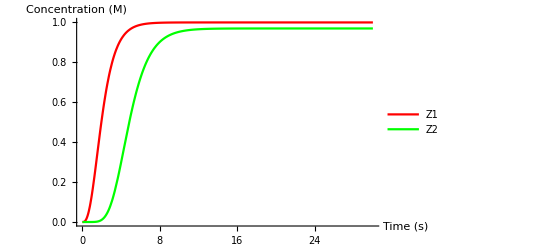

```mathematica
tmax=30;
rsys=CRNfulladder[X1,X2,X3,Z1,Z2];
sol=SimulateRxnsys[Join[rsys,{conc[X1,1],conc[X2,1],conc[X3,1]}],tmax];
Plot[Evaluate[{Z1[t],Z2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Green},{Blue},{Black},{Purple}},PlotLegends->{Z1,Z2},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

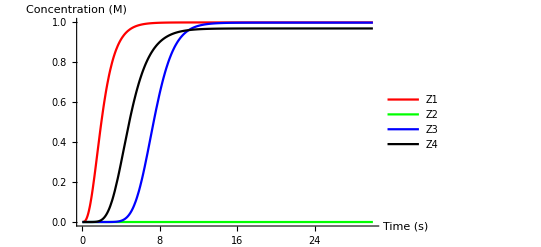

```mathematica
tmax=30;
rsys=CRN3bitadder[X1,X2,X3,Y1,Y2,Y3,Z1,Z2,Z3,Z4];
sol=SimulateRxnsys[Join[rsys,{conc[X1,0],conc[X2,1],conc[X3,1],conc[Y1,1],conc[Y2,1],conc[Y3,1]}],tmax];
Plot[Evaluate[{Z1[t],Z2[t],Z3[t],Z4[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Green},{Blue},{Black},{Purple}},PlotLegends->{Z1,Z2,Z3,Z4},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
{X1[tmax]+2*X2[tmax]+4*X3[tmax]}/.sol
{Y1[tmax]+2*Y2[tmax]+4*Y3[tmax]}/.sol
{Z1[tmax]+2*Z2[tmax]+4*Z3[tmax]+8*Z4[tmax]}/.sol
```

{6.}

{7.}

{12.7545}

```mathematica
tmax=200;
With[{ϵ=0.15},
TableForm[Flatten[
Table[{x1,x2,x3,y1,y2,y3,Z1[tmax],Z2[tmax],Z3[tmax],Z4[tmax]}/.SimulateRxnsys[Join[CRN3bitadder[X1,X2,X3,Y1,Y2,Y3,Z1,Z2,Z3,Z4],{conc[X1,x1],conc[X2,x2],conc[X3,x3],conc[Y1,y1],conc[Y2,y2],conc[Y3,y3]}],tmax],
{x1,{ϵ,1-ϵ}},{x2,{ϵ,1-ϵ}},{x3,{ϵ,1-ϵ}},
{y1,{ϵ,1-ϵ}},{y2,{ϵ,1-ϵ}},{y3,{ϵ,1-ϵ}}],
5],
TableHeadings->{None,{X1,X2,X3,Y1,Y2,Y3,Z1,Z2,Z3,Z4}}]]
```

X1 | X2 | X3 | Y1 | Y2 | Y3 | Z1 | Z2 | Z3 | Z4
0.15 | 0.15 | 0.15 | 0.15 | 0.15 | 0.15 | 0.104871 | 0.0136593 | 0.0135399 | 2.02783×10^-7
0.15 | 0.15 | 0.15 | 0.15 | 0.15 | 0.85 | 0.104871 | 0.0136593 | 0.98646 | 0.000327263
0.15 | 0.15 | 0.15 | 0.15 | 0.85 | 0.15 | 0.104871 | 0.986341 | 0.0136136 | 2.02784×10^-7
0.15 | 0.15 | 0.15 | 0.15 | 0.85 | 0.85 | 0.104871 | 0.986341 | 0.986386 | 0.000327266
0.15 | 0.15 | 0.15 | 0.85 | 0.15 | 0.15 | 0.895129 | 0.0187322 | 0.0135399 | 2.02783×10^-7
0.15 | 0.15 | 0.15 | 0.85 | 0.15 | 0.85 | 0.895129 | 0.0187322 | 0.98646 | 0.000327263
0.15 | 0.15 | 0.15 | 0.85 | 0.85 | 0.15 | 0.895129 | 0.981268 | 0.0136162 | 2.02784×10^-7
0.15 | 0.15 | 0.15 | 0.85 | 0.85 | 0.85 | 0.895129 | 0.981268 | 0.986384 | 0.000327266
0.15 | 0.15 | 0.85 | 0.15 | 0.15 | 0.15 | 0.104871 | 0.0136593 | 0.98646 | 0.000327263
0.15 | 0.15 | 0.85 | 0.15 | 0.15 | 0.85 | 0.104871 | 0.0136593 | 0.0135399 | 0.890856
0.15 | 0.15 | 0.85 | 0.15 | 0.85 | 0.15 | 0.104871 | 0.986341 | 0.986386 | 0.000327266
0.15 | 0.15 | 0.85 | 0.15 | 0.85 | 0.85 | 0.104871 | 0.986341 | 0.0136136 | 0.890856
0.15 | 0.15 | 0.85 | 0.85 | 0.15 | 0.15 | 0.895129 | 0.0187322 | 0.98646 | 0.000327263
0.15 | 0.15 | 0.85 | 0.85 | 0.15 | 0.85 | 0.895129 | 0.0187322 | 0.0135399 | 0.890856
0.15 | 0.15 | 0.85 | 0.85 | 0.85 | 0.15 | 0.895129 | 0.981268 | 0.986384 | 0.000327266
0.15 | 0.15 | 0.85 | 0.85 | 0.85 | 0.85 | 0.895129 | 0.981268 | 0.0136162 | 0.890856
0.15 | 0.85 | 0.15 | 0.15 | 0.15 | 0.15 | 0.104871 | 0.986341 | 0.0136136 | 2.02784×10^-7
0.15 | 0.85 | 0.15 | 0.15 | 0.15 | 0.85 | 0.104871 | 0.986341 | 0.986386 | 0.000327266
0.15 | 0.85 | 0.15 | 0.15 | 0.85 | 0.15 | 0.104871 | 0.0136593 | 0.947123 | 0.0000896898
0.15 | 0.85 | 0.15 | 0.15 | 0.85 | 0.85 | 0.104871 | 0.0136593 | 0.052877 | 0.951765
0.15 | 0.85 | 0.15 | 0.85 | 0.15 | 0.15 | 0.895129 | 0.981268 | 0.0136162 | 2.02784×10^-7
0.15 | 0.85 | 0.15 | 0.85 | 0.15 | 0.85 | 0.895129 | 0.981268 | 0.986384 | 0.000327266
0.15 | 0.85 | 0.15 | 0.85 | 0.85 | 0.15 | 0.895129 | 0.0187322 | 0.947125 | 0.0000896916
0.15 | 0.85 | 0.15 | 0.85 | 0.85 | 0.85 | 0.895129 | 0.0187322 | 0.0528748 | 0.951767
0.15 | 0.85 | 0.85 | 0.15 | 0.15 | 0.15 | 0.104871 | 0.986341 | 0.986386 | 0.000327266
0.15 | 0.85 | 0.85 | 0.15 | 0.15 | 0.85 | 0.104871 | 0.986341 | 0.0136136 | 0.890856
0.15 | 0.85 | 0.85 | 0.15 | 0.85 | 0.15 | 0.104871 | 0.0136593 | 0.052877 | 0.951765
0.15 | 0.85 | 0.85 | 0.15 | 0.85 | 0.85 | 0.104871 | 0.0136593 | 0.947123 | 0.899673
0.15 | 0.85 | 0.85 | 0.85 | 0.15 | 0.15 | 0.895129 | 0.981268 | 0.986384 | 0.000327266
0.15 | 0.85 | 0.85 | 0.85 | 0.15 | 0.85 | 0.895129 | 0.981268 | 0.0136162 | 0.890856
0.15 | 0.85 | 0.85 | 0.85 | 0.85 | 0.15 | 0.895129 | 0.0187322 | 0.0528748 | 0.951767
0.15 | 0.85 | 0.85 | 0.85 | 0.85 | 0.85 | 0.895129 | 0.0187322 | 0.947125 | 0.899673
0.85 | 0.15 | 0.15 | 0.15 | 0.15 | 0.15 | 0.895129 | 0.0187322 | 0.0135399 | 2.02783×10^-7
0.85 | 0.15 | 0.15 | 0.15 | 0.15 | 0.85 | 0.895129 | 0.0187322 | 0.98646 | 0.000327263
0.85 | 0.15 | 0.15 | 0.15 | 0.85 | 0.15 | 0.895129 | 0.981268 | 0.0136162 | 2.02784×10^-7
0.85 | 0.15 | 0.15 | 0.15 | 0.85 | 0.85 | 0.895129 | 0.981268 | 0.986384 | 0.000327266
0.85 | 0.15 | 0.15 | 0.85 | 0.15 | 0.15 | 0.104871 | 0.936598 | 0.0135583 | 2.02783×10^-7
0.85 | 0.15 | 0.15 | 0.85 | 0.15 | 0.85 | 0.104871 | 0.936598 | 0.986442 | 0.000327263
0.85 | 0.15 | 0.15 | 0.85 | 0.85 | 0.15 | 0.104871 | 0.0634017 | 0.970447 | 0.00011489
0.85 | 0.15 | 0.15 | 0.85 | 0.85 | 0.85 | 0.104871 | 0.0634017 | 0.0295535 | 0.965167
0.85 | 0.15 | 0.85 | 0.15 | 0.15 | 0.15 | 0.895129 | 0.0187322 | 0.98646 | 0.000327263
0.85 | 0.15 | 0.85 | 0.15 | 0.15 | 0.85 | 0.895129 | 0.0187322 | 0.0135399 | 0.890856
0.85 | 0.15 | 0.85 | 0.15 | 0.85 | 0.15 | 0.895129 | 0.981268 | 0.986384 | 0.000327266
0.85 | 0.15 | 0.85 | 0.15 | 0.85 | 0.85 | 0.895129 | 0.981268 | 0.0136162 | 0.890856
0.85 | 0.15 | 0.85 | 0.85 | 0.15 | 0.15 | 0.104871 | 0.936598 | 0.986442 | 0.000327263
0.85 | 0.15 | 0.85 | 0.85 | 0.15 | 0.85 | 0.104871 | 0.936598 | 0.0135583 | 0.890856
0.85 | 0.15 | 0.85 | 0.85 | 0.85 | 0.15 | 0.104871 | 0.0634017 | 0.0295535 | 0.965167
0.85 | 0.15 | 0.85 | 0.85 | 0.85 | 0.85 | 0.104871 | 0.0634017 | 0.970447 | 0.900846
0.85 | 0.85 | 0.15 | 0.15 | 0.15 | 0.15 | 0.895129 | 0.981268 | 0.0136162 | 2.02784×10^-7
0.85 | 0.85 | 0.15 | 0.15 | 0.15 | 0.85 | 0.895129 | 0.981268 | 0.986384 | 0.000327266
0.85 | 0.85 | 0.15 | 0.15 | 0.85 | 0.15 | 0.895129 | 0.0187322 | 0.947125 | 0.0000896916
0.85 | 0.85 | 0.15 | 0.15 | 0.85 | 0.85 | 0.895129 | 0.0187322 | 0.0528748 | 0.951767
0.85 | 0.85 | 0.15 | 0.85 | 0.15 | 0.15 | 0.104871 | 0.0634017 | 0.970447 | 0.00011489
0.85 | 0.85 | 0.15 | 0.85 | 0.15 | 0.85 | 0.104871 | 0.0634017 | 0.0295535 | 0.965167
0.85 | 0.85 | 0.15 | 0.85 | 0.85 | 0.15 | 0.104871 | 0.936598 | 0.951323 | 0.0000933013
0.85 | 0.85 | 0.15 | 0.85 | 0.85 | 0.85 | 0.104871 | 0.936598 | 0.0486767 | 0.954408
0.85 | 0.85 | 0.85 | 0.15 | 0.15 | 0.15 | 0.895129 | 0.981268 | 0.986384 | 0.000327266
0.85 | 0.85 | 0.85 | 0.15 | 0.15 | 0.85 | 0.895129 | 0.981268 | 0.0136162 | 0.890856
0.85 | 0.85 | 0.85 | 0.15 | 0.85 | 0.15 | 0.895129 | 0.0187322 | 0.0528748 | 0.951767
0.85 | 0.85 | 0.85 | 0.15 | 0.85 | 0.85 | 0.895129 | 0.0187322 | 0.947125 | 0.899673
0.85 | 0.85 | 0.85 | 0.85 | 0.15 | 0.15 | 0.104871 | 0.0634017 | 0.0295535 | 0.965167
0.85 | 0.85 | 0.85 | 0.85 | 0.15 | 0.85 | 0.104871 | 0.0634017 | 0.970447 | 0.900846
0.85 | 0.85 | 0.85 | 0.85 | 0.85 | 0.15 | 0.104871 | 0.936598 | 0.0486767 | 0.954408
0.85 | 0.85 | 0.85 | 0.85 | 0.85 | 0.85 | 0.104871 | 0.936598 | 0.951323 | 0.899851

We see that all the output values are within the correct range for ϵ of 0.15. We can also check that the addition circuit CRN has the correct outputs.

```mathematica
With[{ϵ=0.15},Flatten[
Table[{If[x1≤ϵ,0,If[x1≥1-ϵ,1,"false"]]+2*If[x2≤ϵ,0,If[x2≥1-ϵ,1,"false"]]+4*If[x3≤ϵ,0,If[x3≥1-ϵ,1,"false"]]+If[y1≤ϵ,0,If[y1≥1-ϵ,1,"false"]]+2*If[y2≤ϵ,0,If[y2≥1-ϵ,1,"false"]]+4*If[y3≤ϵ,0,If[y3≥1-ϵ,1,"false"]]==If[Z1[tmax]≤ϵ,0,If[Z1[tmax]≥1-ϵ,1,"false"]]+2*If[Z2[tmax]≤ϵ,0,If[Z2[tmax]≥1-ϵ,1,"false"]]+4*If[Z3[tmax]≤ϵ,0,If[Z3[tmax]≥1-ϵ,1,"false"]]+8*If[Z4[tmax]≤ϵ,0,If[Z4[tmax]≥1-ϵ,1,"false"]]}/.SimulateRxnsys[Join[CRN3bitadder[X1,X2,X3,Y1,Y2,Y3,Z1,Z2,Z3,Z4],{conc[X1,x1],conc[X2,x2],conc[X3,x3],conc[Y1,y1],conc[Y2,y2],conc[Y3,y3]}],tmax],
{x1,{ϵ,1-ϵ}},{x2,{ϵ,1-ϵ}},{x3,{ϵ,1-ϵ}},
{y1,{ϵ,1-ϵ}},{y2,{ϵ,1-ϵ}},{y3,{ϵ,1-ϵ}}],
5]]
```

{{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True}}

We know that the ϵ value could be larger but not smaller than the value for the individual gates, because we are given inputs <= ϵ or >=(1- ϵ) and for each gate the output is guaranteed to be in these values; therefore, the inputs to the next gates in the circuit will also be within the required range. Since it must work at each gate, we know that for the whole circuit, the ϵ value could not be smaller than what we found previously. It could be larger if we have other gates with a larger ϵ value in the circuit that reduce the inputs to a level below the xor ϵ by the time it reaches the xor gate (or reduces it back below ϵ after going through the xor gate).

We see that it works for ϵ=0.18 which is bigger than that of 0.17 for the And gate.

```mathematica
With[{ϵ=0.18},Flatten[
Table[{If[x1≤ϵ,0,If[x1≥1-ϵ,1,"false"]]+2*If[x2≤ϵ,0,If[x2≥1-ϵ,1,"false"]]+4*If[x3≤ϵ,0,If[x3≥1-ϵ,1,"false"]]+If[y1≤ϵ,0,If[y1≥1-ϵ,1,"false"]]+2*If[y2≤ϵ,0,If[y2≥1-ϵ,1,"false"]]+4*If[y3≤ϵ,0,If[y3≥1-ϵ,1,"false"]]==If[Z1[tmax]≤ϵ,0,If[Z1[tmax]≥1-ϵ,1,"false"]]+2*If[Z2[tmax]≤ϵ,0,If[Z2[tmax]≥1-ϵ,1,"false"]]+4*If[Z3[tmax]≤ϵ,0,If[Z3[tmax]≥1-ϵ,1,"false"]]+8*If[Z4[tmax]≤ϵ,0,If[Z4[tmax]≥1-ϵ,1,"false"]]}/.SimulateRxnsys[Join[CRN3bitadder[X1,X2,X3,Y1,Y2,Y3,Z1,Z2,Z3,Z4],{conc[X1,x1],conc[X2,x2],conc[X3,x3],conc[Y1,y1],conc[Y2,y2],conc[Y3,y3]}],tmax],
{x1,{ϵ,1-ϵ}},{x2,{ϵ,1-ϵ}},{x3,{ϵ,1-ϵ}},
{y1,{ϵ,1-ϵ}},{y2,{ϵ,1-ϵ}},{y3,{ϵ,1-ϵ}}],
5]]
```

{{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True}}

```mathematica
With[{ϵ=0.19},Flatten[
Table[{If[x1≤ϵ,0,If[x1≥1-ϵ,1,"false"]]+2*If[x2≤ϵ,0,If[x2≥1-ϵ,1,"false"]]+4*If[x3≤ϵ,0,If[x3≥1-ϵ,1,"false"]]+If[y1≤ϵ,0,If[y1≥1-ϵ,1,"false"]]+2*If[y2≤ϵ,0,If[y2≥1-ϵ,1,"false"]]+4*If[y3≤ϵ,0,If[y3≥1-ϵ,1,"false"]]==If[Z1[tmax]≤ϵ,0,If[Z1[tmax]≥1-ϵ,1,"false"]]+2*If[Z2[tmax]≤ϵ,0,If[Z2[tmax]≥1-ϵ,1,"false"]]+4*If[Z3[tmax]≤ϵ,0,If[Z3[tmax]≥1-ϵ,1,"false"]]+8*If[Z4[tmax]≤ϵ,0,If[Z4[tmax]≥1-ϵ,1,"false"]]}/.SimulateRxnsys[Join[CRN3bitadder[X1,X2,X3,Y1,Y2,Y3,Z1,Z2,Z3,Z4],{conc[X1,x1],conc[X2,x2],conc[X3,x3],conc[Y1,y1],conc[Y2,y2],conc[Y3,y3]}],tmax],
{x1,{ϵ,1-ϵ}},{x2,{ϵ,1-ϵ}},{x3,{ϵ,1-ϵ}},
{y1,{ϵ,1-ϵ}},{y2,{ϵ,1-ϵ}},{y3,{ϵ,1-ϵ}}],
5]]
```

{{True},{True},{True},{True},{True},{True},{True},{True},{True},{8==8 false},{True},{10==2+8 false},{True},{9==1+8 false},{True},{11==3+8 false},{True},{True},{True},{True},{True},{True},{True},{True},{True},{10==2+8 false},{True},{True},{True},{11==3+8 false},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{9==1+8 false},{True},{11==3+8 false},{True},{10==2+8 false},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{11==3+8 false},{True},{True},{True},{True},{True},{True}}

## Part 2: Deriving a CRN that does gradient descent to a line attractor.

Gradient descent is often used in a context where the local and global minima are points, such as the bottom of a parabola.  But this needn’t necessarily be the case.  A “line attractor”, for example, occurs when dynamics will approach and come to a halt wherever it hits a one-dimensional curve of steady-state solution.  Suppose we want a system that is “happy” whenever 
	a x^2+b x y+c y^2=d 
where all variables have arbitrary positive or negative real values.  For example, if a=1, b=0, c=1, and d=1, then the “happy” solutions occur for (x,y) on a unit circle.  We want a CRN that will accept dual-rail input via the concentrations of species a[pos], a[neg], b[pos], b[neg], c[pos], c[neg], d[pos], and d[neg], and (without changing the inputs) will adjust dual-rail dynamical species x[pos], x[neg], y[pos], y[neg] until the constraint is satisfied, and then will happily stop. (We don’t use C and D as species symbols because they have built-in meaning for Mathematica, so we just go for lower-case throughout.)  

(a) Write down a suitable loss function L in terms of the real variables a,b,c,d,x,y and derive polynomial ODEs for gradient descent of L that will bring the system to the line attractor.  You will shortly derive a CRN from L, but don’t do that yet.  First imagine what this CRN could do, before you build it and see.  (Prediction should be prediction, so don’t go back and revise this section after you’ve built it and actually see what it will do.)  What are different classes of behaviors you might see, depending on the constant values for a,b,c,d? (We’re looking for exploration here, not rigorous classification.) Are there any situations for which the gradient descent dynamics will not converge?  What might happen if rather than being constants,  a,b,c,d are time-varying inputs from an upstream process?  What if there is a slight “wind” blowing the “marble”, e.g. due to a slow leak reaction, that adds a tiny extra push to the (x,y) motion?

For the example, if a=1, b=0, c=1, and d=1, we see that this CRN would descent from its starting point down to a point on the unit circle. In general, we can predict that the CRN will converge down the gradient to a local minima. Depending on the constants, we could see behaviors where the gradient descents directly towards the local/global minima or we could see the gradient follow a very indirect path towards convergence. We could also see behaviors where the gradient is stuck on a flat surface and the gradient descent would not converge unless there was an additional tiny extra push to the (x, y) motion that would get it off the flat surface. If the constants are actually time-varying inputs, then we could see the minima change and the gradient descent to alter its path and direction.

```mathematica
Clear[a,b,c,d,x,y]
```

```mathematica
Manipulate[ContourPlot[{ 
a x^2+b x y+c y^2==d
},{x,-3,3},{y,-3,3},FrameLabel->{x,y},PlotLegends->{"eqn"}],{{a,1},0,3},{{b,0},0,3},{{c,1},0,3},{{d,1},0,3}]
```

```mathematica
L=(d-a x^2-b x y-c y^2)^2
```

(d-a x^2-b x y-c y^2)^2

```mathematica
Ltest=(d-a x^2-b x y-c y^2)^2/.{a->1,b->0,c->1,d->1}
```

(1-x^2-y^2)^2

```mathematica
Plot3D[Ltest,{x,-3,3},{y,-3,3},AxesLabel->{x,y}]
```

-Graphics3D-

```mathematica
{D[L,x],D[L,y]}
```

{2 (-2 a x-b y) (d-a x^2-b x y-c y^2),2 (-b x-2 c y) (d-a x^2-b x y-c y^2)}

```mathematica
diffeq={
x'[t]==-(D[L,x]/.{x->x[t],y->y[t]}),
y'[t]==-(D[L,y]/.{x->x[t],y->y[t]}),
x[0]==2,y[0]==2
}
```

{x'[t]==-2 (-2 a x[t]-b y[t]) (d-a x[t]^2-b x[t] y[t]-c y[t]^2),y'[t]==-2 (-b x[t]-2 c y[t]) (d-a x[t]^2-b x[t] y[t]-c y[t]^2),x[0]==2,y[0]==2}

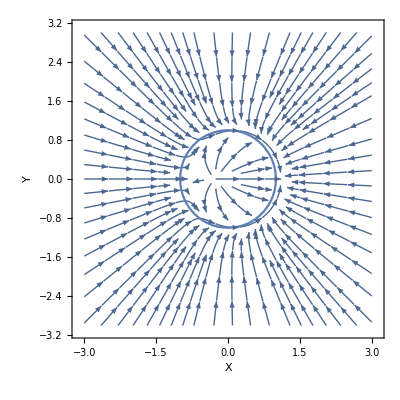

```mathematica
With[{a=1,b=0,c=1,d=1},Show[
StreamPlot[{d-2 (-2 a x-b y) (d-a x^2-b x y-c y^2),-2 (-b x-2 c y) (d-a x^2-b x y-c y^2)},{x,-3,3},{y,-3,3},FrameLabel->{X,Y}],
ContourPlot[{a x^2+b x y+c y^2==d},{x,-3,3},{y,-3,3}]
]]
```

```mathematica
{min1,sol1}=NMinimize[{Ltest,x>0&&y>0},{x,y}]
```

{1.2326×10^-32,{x→0.236688,y→0.971586}}

```mathematica
{min2,sol2}=NMinimize[{Ltest,x<.5&&y<.5},{x,y}]
```

{1.92593×10^-34,{x→-0.964116,y→-0.265483}}

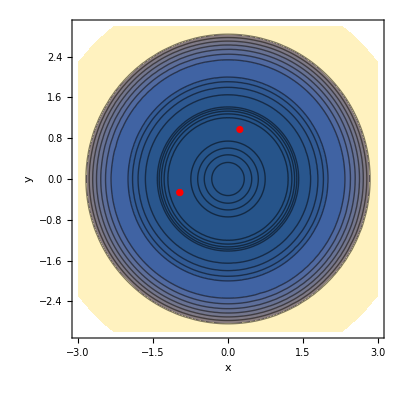

```mathematica
Show[
ContourPlot[Ltest,{x,-3,3},{y,-3,3},FrameLabel->{x,y},Contours->{0,.2,.4,.6,.8}~Join~Range[1,10,2]~Join~Range[20,50,5]],
ListPlot[{x,y}/.{{sol1,sol2}},PlotStyle->Red]]
```

(b) Convert these ODEs into a CRN, and show by simulation that it will behave as expected.  Consider a few different settings for the inputs a,b,c,d.  If you are very comfortable with automating symbol manipulation, such that you don’t have to do things by hand, then go ahead and represent a,b,c,d via dual-rail chemical species.  But be warned that it will result in hundreds of reactions.  So it is recommended -- and full credit will be given -- if you just plug in the constants and  derive a hard-coded CRN (which will still be something like 26 reactions).   Show simulations in phase space (i.e. trajectories in the (x,y) plane) with the final point marked.

x'[t]==-2 (-2 a x[t]-b y[t]) (d-a x[t]^2-b x[t] y[t]-c y[t]^2),y'[t]==-2 (-b x[t]-2 c y[t]) (d-a x[t]^2-b x[t] y[t]-c y[t]^2)

```mathematica
Expand[-2 (-2 a (x1-x2)-b (y1-y2)) (d-a (x1-x2)^2-b (x1-x2) (y1-y2)-c (y1-y2)^2)]
Expand[-2 (-b (x1-x2)-2 c (y1-y2)) (d-a (x1-x2)^2-b (x1-x2) (y1-y2)-c (y1-y2)^2)]
```

4 a d x1-4 a^2 x1^3-4 a d x2+12 a^2 x1^2 x2-12 a^2 x1 x2^2+4 a^2 x2^3+2 b d y1-6 a b x1^2 y1+12 a b x1 x2 y1-6 a b x2^2 y1-2 b^2 x1 y1^2-4 a c x1 y1^2+2 b^2 x2 y1^2+4 a c x2 y1^2-2 b c y1^3-2 b d y2+6 a b x1^2 y2-12 a b x1 x2 y2+6 a b x2^2 y2+4 b^2 x1 y1 y2+8 a c x1 y1 y2-4 b^2 x2 y1 y2-8 a c x2 y1 y2+6 b c y1^2 y2-2 b^2 x1 y2^2-4 a c x1 y2^2+2 b^2 x2 y2^2+4 a c x2 y2^2-6 b c y1 y2^2+2 b c y2^3

2 b d x1-2 a b x1^3-2 b d x2+6 a b x1^2 x2-6 a b x1 x2^2+2 a b x2^3+4 c d y1-2 b^2 x1^2 y1-4 a c x1^2 y1+4 b^2 x1 x2 y1+8 a c x1 x2 y1-2 b^2 x2^2 y1-4 a c x2^2 y1-6 b c x1 y1^2+6 b c x2 y1^2-4 c^2 y1^3-4 c d y2+2 b^2 x1^2 y2+4 a c x1^2 y2-4 b^2 x1 x2 y2-8 a c x1 x2 y2+2 b^2 x2^2 y2+4 a c x2^2 y2+12 b c x1 y1 y2-12 b c x2 y1 y2+12 c^2 y1^2 y2-6 b c x1 y2^2+6 b c x2 y2^2-12 c^2 y1 y2^2+4 c^2 y2^3

```mathematica
kf=1000;
a=1;
b=0;
c=1;
d=1;
base[X1_,X2_,Y1_,Y2_]:={rxn[X1+X2,0,kf],rxn[Y1+Y2,0,kf]}
sysx[X1_,X2_,Y1_,Y2_]:={rxn[X1,X1+X1,4a d],rxn[3X1,3X1+X2,4a^2],rxn[X2,X2+X2,4a d],rxn[2X1+X2,2X1+X2+X1,12 a^2],rxn[X1+2X2,X1+2X2+X2,12 a^2],rxn[3X2,3X2+X1,4a^2],rxn[Y1,Y1+X1,2b d],rxn[2X1+Y1,2X1+Y1+X2,6a b],rxn[X1+X2+Y1,X1+X2+Y1+X1,12a b],rxn[2X2+Y1,2X2+Y1+X2,6a b],rxn[X1+2Y1,X1+2Y1+X2,2b^2+4a c],rxn[X2+2Y1,X2+2Y1+X1,2b^2+4a c],rxn[3Y1,3Y1+X2,2b c],rxn[Y2,Y2+X2,2b d],rxn[2X1+Y2,2X1+Y2+X1,6a b],rxn[X1+X2+Y2,X1+X2+Y2+X2,12a b],rxn[2X2+Y2,2X2+Y2+X1,6a b],rxn[X1+Y1+Y2,X1+Y1+Y2+X1,4b^2+8a c],rxn[X2+Y1+Y2,X2+Y1+Y2+X2,4b^2+8a c],rxn[2Y1+Y2,2Y1+Y2+X1,6b c],rxn[X1+2Y2,X1+2Y2+X2,2b^2+4a c],rxn[X2+2Y2,X2+2Y2+X1,2b^2+4a c],rxn[Y1+2Y2,Y1+2Y2+X2,6b c],rxn[3Y2,3Y2+X1,2b c]}
sysy[X1_,X2_,Y1_,Y2_]:={rxn[X1,X1+Y1,2b d],rxn[3X1,3X1+Y2,2a b],rxn[X2,X2+Y2,2b d],rxn[2X1+X2,2X1+X2+Y1,6a b],rxn[X1+2X2,X1+2X2+Y2,6a b],rxn[3X2,3X2+Y1,2a b],rxn[Y1,Y1+Y1,4c d],rxn[2X1+Y1,2X1+Y1+Y2,2b^2+4a c],rxn[X1+X2+Y1,X1+X2+Y1+Y1,4b^2+8a c],rxn[2X2+Y1,2X2+Y1+Y2,2b^2+4a c],rxn[X1+2Y1,X1+2Y1+Y2,6b c],rxn[X2+2Y1,X2+2Y1+Y1,6b c],rxn[3Y1,3Y1+Y2,4c^2],rxn[Y2,Y2+Y2,4c d],rxn[2X1+Y2,2X1+Y2+Y1,2b^2+4a c],rxn[X1+X2+Y2,X1+X2+Y2+Y2,4b^2-8a c],rxn[2X2+Y2,2X2+Y2+Y1,2b^2+4a c],rxn[X1+Y1+Y2,X1+Y1+Y2+Y1,12b c],rxn[X2+Y1+Y2,X2+Y1+Y2+Y2,12b c],rxn[2Y1+Y2,2Y1+Y2+Y1,12c^2],rxn[X1+2Y2,X1+2Y2+Y2,6b c],rxn[X2+2Y2,X2+2Y2+Y1,6b c],rxn[Y1+2Y2,Y1+2Y2+Y2,12c^2],rxn[3Y2,3Y2+Y1,4c^2]}
rsys=Flatten[{base[X1,X2,Y1,Y2],sysx[X1,X2,Y1,Y2],sysy[X1,X2,Y1,Y2]}]
```

{  X1+X2⟶^10000,  Y1+Y2⟶^10000,  X1⟶^42 X1,  3 X1⟶^43 X1+X2,  X2⟶^42 X2,  2 X1+X2⟶^123 X1+X2,  X1+2 X2⟶^12X1+3 X2,  3 X2⟶^4X1+3 X2,  Y1⟶^0X1+Y1,  2 X1+Y1⟶^02 X1+X2+Y1,  X1+X2+Y1⟶^02 X1+X2+Y1,  2 X2+Y1⟶^03 X2+Y1,  X1+2 Y1⟶^4X1+X2+2 Y1,  X2+2 Y1⟶^4X1+X2+2 Y1,  3 Y1⟶^0X2+3 Y1,  Y2⟶^0X2+Y2,  2 X1+Y2⟶^03 X1+Y2,  X1+X2+Y2⟶^0X1+2 X2+Y2,  2 X2+Y2⟶^0X1+2 X2+Y2,  X1+Y1+Y2⟶^82 X1+Y1+Y2,  X2+Y1+Y2⟶^82 X2+Y1+Y2,  2 Y1+Y2⟶^0X1+2 Y1+Y2,  X1+2 Y2⟶^4X1+X2+2 Y2,  X2+2 Y2⟶^4X1+X2+2 Y2,  Y1+2 Y2⟶^0X2+Y1+2 Y2,  3 Y2⟶^0X1+3 Y2,  X1⟶^0X1+Y1,  3 X1⟶^03 X1+Y2,  X2⟶^0X2+Y2,  2 X1+X2⟶^02 X1+X2+Y1,  X1+2 X2⟶^0X1+2 X2+Y2,  3 X2⟶^03 X2+Y1,  Y1⟶^42 Y1,  2 X1+Y1⟶^42 X1+Y1+Y2,  X1+X2+Y1⟶^8X1+X2+2 Y1,  2 X2+Y1⟶^42 X2+Y1+Y2,  X1+2 Y1⟶^0X1+2 Y1+Y2,  X2+2 Y1⟶^0X2+3 Y1,  3 Y1⟶^43 Y1+Y2,  Y2⟶^42 Y2,  2 X1+Y2⟶^42 X1+Y1+Y2,  X1+X2+Y2⟶^-8X1+X2+2 Y2,  2 X2+Y2⟶^42 X2+Y1+Y2,  X1+Y1+Y2⟶^0X1+2 Y1+Y2,  X2+Y1+Y2⟶^0X2+Y1+2 Y2,  2 Y1+Y2⟶^123 Y1+Y2,  X1+2 Y2⟶^0X1+3 Y2,  X2+2 Y2⟶^0X2+Y1+2 Y2,  Y1+2 Y2⟶^12Y1+3 Y2,  3 Y2⟶^4Y1+3 Y2}

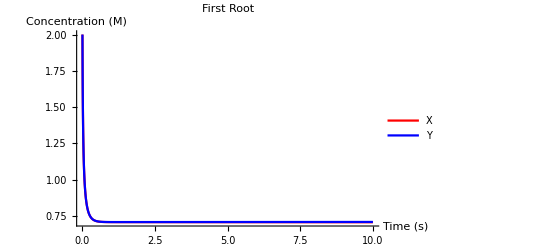

```mathematica
tmax=10;
sol=SimulateRxnsys[Join[rsys,{conc[X1,2],conc[X2,0],conc[Y1,2],conc[Y2,0]}],tmax];
Plot[Evaluate[{X1[t]-X2[t],Y1[t]-Y2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Blue},{LightRed},{LightBlue},{Green},{Black}},PlotLegends->{X,Y},
AxesLabel->{"Time (s)","Concentration (M)"},PlotLabel->"First Root"]
```

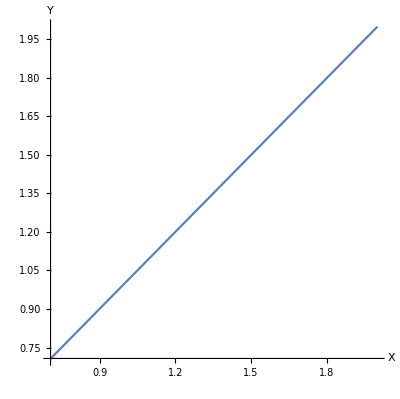

```mathematica
ParametricPlot[Evaluate[{X1[t]-X2[t],Y1[t]-Y2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},AxesLabel->{X,Y}]
```

```mathematica
soln:=NDSolve[{
x'[t]==-(D[L,x]/.{x->x[t],y->y[t]}),
y'[t]==-(D[L,y]/.{x->x[t],y->y[t]}),
x[0]==2,y[0]==2
},{x,y},{t,0,tmax}]
```

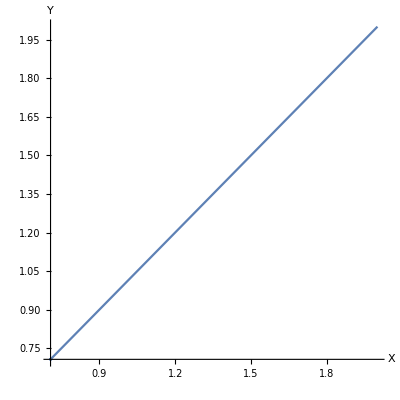

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.soln],{t,0,tmax},PlotRange->{All,All},AxesLabel->{X,Y}]
```

```mathematica
sol=NDSolve[diffeq,{x,y},{t,0,10}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

```mathematica
Show[Plot3D[L,{x,-3,3},{y,-3,3},AxesLabel->{x,y}],ParametricPlot3D[{x[t],y[t],L/.{x->x[t],y->y[t]}}/.sol,{t,0,10}]]
```

-Graphics3D-

```mathematica
kf=1000;
a=1;
b=1;
c=1;
d=1;
base[X1_,X2_,Y1_,Y2_]:={rxn[X1+X2,0,kf],rxn[Y1+Y2,0,kf]}
sysx[X1_,X2_,Y1_,Y2_]:={rxn[X1,X1+X1,4a d],rxn[3X1,3X1+X2,4a^2],rxn[X2,X2+X2,4a d],rxn[2X1+X2,2X1+X2+X1,12 a^2],rxn[X1+2X2,X1+2X2+X2,12 a^2],rxn[3X2,3X2+X1,4a^2],rxn[Y1,Y1+X1,2b d],rxn[2X1+Y1,2X1+Y1+X2,6a b],rxn[X1+X2+Y1,X1+X2+Y1+X1,12a b],rxn[2X2+Y1,2X2+Y1+X2,6a b],rxn[X1+2Y1,X1+2Y1+X2,2b^2+4a c],rxn[X2+2Y1,X2+2Y1+X1,2b^2+4a c],rxn[3Y1,3Y1+X2,2b c],rxn[Y2,Y2+X2,2b d],rxn[2X1+Y2,2X1+Y2+X1,6a b],rxn[X1+X2+Y2,X1+X2+Y2+X2,12a b],rxn[2X2+Y2,2X2+Y2+X1,6a b],rxn[X1+Y1+Y2,X1+Y1+Y2+X1,4b^2+8a c],rxn[X2+Y1+Y2,X2+Y1+Y2+X2,4b^2+8a c],rxn[2Y1+Y2,2Y1+Y2+X1,6b c],rxn[X1+2Y2,X1+2Y2+X2,2b^2+4a c],rxn[X2+2Y2,X2+2Y2+X1,2b^2+4a c],rxn[Y1+2Y2,Y1+2Y2+X2,6b c],rxn[3Y2,3Y2+X1,2b c]}
sysy[X1_,X2_,Y1_,Y2_]:={rxn[X1,X1+Y1,2b d],rxn[3X1,3X1+Y2,2a b],rxn[X2,X2+Y2,2b d],rxn[2X1+X2,2X1+X2+Y1,6a b],rxn[X1+2X2,X1+2X2+Y2,6a b],rxn[3X2,3X2+Y1,2a b],rxn[Y1,Y1+Y1,4c d],rxn[2X1+Y1,2X1+Y1+Y2,2b^2+4a c],rxn[X1+X2+Y1,X1+X2+Y1+Y1,4b^2+8a c],rxn[2X2+Y1,2X2+Y1+Y2,2b^2+4a c],rxn[X1+2Y1,X1+2Y1+Y2,6b c],rxn[X2+2Y1,X2+2Y1+Y1,6b c],rxn[3Y1,3Y1+Y2,4c^2],rxn[Y2,Y2+Y2,4c d],rxn[2X1+Y2,2X1+Y2+Y1,2b^2+4a c],rxn[X1+X2+Y2,X1+X2+Y2+Y2,4b^2-8a c],rxn[2X2+Y2,2X2+Y2+Y1,2b^2+4a c],rxn[X1+Y1+Y2,X1+Y1+Y2+Y1,12b c],rxn[X2+Y1+Y2,X2+Y1+Y2+Y2,12b c],rxn[2Y1+Y2,2Y1+Y2+Y1,12c^2],rxn[X1+2Y2,X1+2Y2+Y2,6b c],rxn[X2+2Y2,X2+2Y2+Y1,6b c],rxn[Y1+2Y2,Y1+2Y2+Y2,12c^2],rxn[3Y2,3Y2+Y1,4c^2]}
rsys=Flatten[{base[X1,X2,Y1,Y2],sysx[X1,X2,Y1,Y2],sysy[X1,X2,Y1,Y2]}]
```

{  X1+X2⟶^10000,  Y1+Y2⟶^10000,  X1⟶^42 X1,  3 X1⟶^43 X1+X2,  X2⟶^42 X2,  2 X1+X2⟶^123 X1+X2,  X1+2 X2⟶^12X1+3 X2,  3 X2⟶^4X1+3 X2,  Y1⟶^2X1+Y1,  2 X1+Y1⟶^62 X1+X2+Y1,  X1+X2+Y1⟶^122 X1+X2+Y1,  2 X2+Y1⟶^63 X2+Y1,  X1+2 Y1⟶^6X1+X2+2 Y1,  X2+2 Y1⟶^6X1+X2+2 Y1,  3 Y1⟶^2X2+3 Y1,  Y2⟶^2X2+Y2,  2 X1+Y2⟶^63 X1+Y2,  X1+X2+Y2⟶^12X1+2 X2+Y2,  2 X2+Y2⟶^6X1+2 X2+Y2,  X1+Y1+Y2⟶^122 X1+Y1+Y2,  X2+Y1+Y2⟶^122 X2+Y1+Y2,  2 Y1+Y2⟶^6X1+2 Y1+Y2,  X1+2 Y2⟶^6X1+X2+2 Y2,  X2+2 Y2⟶^6X1+X2+2 Y2,  Y1+2 Y2⟶^6X2+Y1+2 Y2,  3 Y2⟶^2X1+3 Y2,  X1⟶^2X1+Y1,  3 X1⟶^23 X1+Y2,  X2⟶^2X2+Y2,  2 X1+X2⟶^62 X1+X2+Y1,  X1+2 X2⟶^6X1+2 X2+Y2,  3 X2⟶^23 X2+Y1,  Y1⟶^42 Y1,  2 X1+Y1⟶^62 X1+Y1+Y2,  X1+X2+Y1⟶^12X1+X2+2 Y1,  2 X2+Y1⟶^62 X2+Y1+Y2,  X1+2 Y1⟶^6X1+2 Y1+Y2,  X2+2 Y1⟶^6X2+3 Y1,  3 Y1⟶^43 Y1+Y2,  Y2⟶^42 Y2,  2 X1+Y2⟶^62 X1+Y1+Y2,  X1+X2+Y2⟶^-4X1+X2+2 Y2,  2 X2+Y2⟶^62 X2+Y1+Y2,  X1+Y1+Y2⟶^12X1+2 Y1+Y2,  X2+Y1+Y2⟶^12X2+Y1+2 Y2,  2 Y1+Y2⟶^123 Y1+Y2,  X1+2 Y2⟶^6X1+3 Y2,  X2+2 Y2⟶^6X2+Y1+2 Y2,  Y1+2 Y2⟶^12Y1+3 Y2,  3 Y2⟶^4Y1+3 Y2}

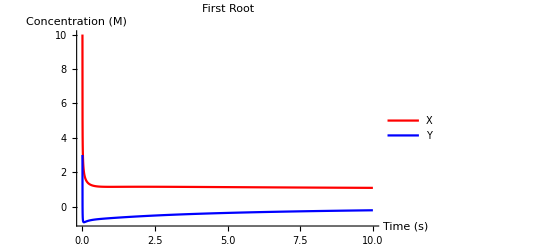

```mathematica
tmax=10;
sol=SimulateRxnsys[Join[rsys,{conc[X1,10],conc[X2,0],conc[Y1,3],conc[Y2,0]}],tmax];
Plot[Evaluate[{X1[t]-X2[t],Y1[t]-Y2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},PlotStyle->{{Red},{Blue},{LightRed},{LightBlue},{Green},{Black}},PlotLegends->{X,Y},
AxesLabel->{"Time (s)","Concentration (M)"},PlotLabel->"First Root"]
```

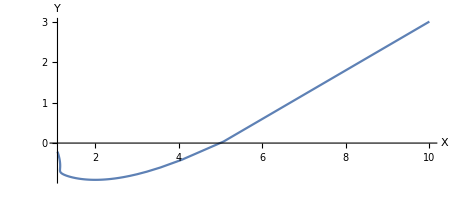

```mathematica
ParametricPlot[Evaluate[{X1[t]-X2[t],Y1[t]-Y2[t]}/.sol],{t,0,tmax},PlotRange->{All,All},AxesLabel->{X,Y}]
```

```mathematica
soln:=NDSolve[{
x'[t]==-(D[L,x]/.{x->x[t],y->y[t]}),
y'[t]==-(D[L,y]/.{x->x[t],y->y[t]}),
x[0]==10,y[0]==3
},{x,y},{t,0,tmax}]
```

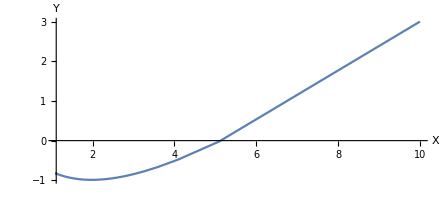

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.soln],{t,0,tmax},PlotRange->{All,All},AxesLabel->{X,Y}]
```

```mathematica
diffeq={
x'[t]==-(D[L,x]/.{x->x[t],y->y[t]}),
y'[t]==-(D[L,y]/.{x->x[t],y->y[t]}),
x[0]==10,y[0]==3
}
```

{x'[t]==-2 (-2 x[t]-y[t]) (1-x[t]^2-x[t] y[t]-y[t]^2),y'[t]==-2 (-x[t]-2 y[t]) (1-x[t]^2-x[t] y[t]-y[t]^2),x[0]==10,y[0]==3}

```mathematica
sol=NDSolve[diffeq,{x,y},{t,0,10}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

```mathematica
Show[Plot3D[L,{x,-10,10},{y,-10,10},AxesLabel->{x,y}],ParametricPlot3D[{x[t],y[t],L/.{x->x[t],y->y[t]}}/.sol,{t,0,10}]]
```

-Graphics3D-

(c) Constrained optimization aims to find the minimum of some f(x,y) subject to a constraint g(x,y)=0.  Suppose both are polynomial.  No need to simulate, but described how a CRN could perform (or at least approximate) such an optimization by modifying L and re-deriving the CRN for gradient descent, perhaps making addition tweaks along the way.  The “natural” approach we’re hoping you find here will work great sometimes, but also come with some potential problems that could arise, such as situations analogous to local minima.  Envision them if you can.

We can modify L to have enormous error for violating the constraint g(x,y)=0, so that doing gradient descent on L will always go to satisfying the constraint then trying to minimize the function f(x,y). We could run into the sort of local minima problem because we go nearly directly to the constraint and after will only move along the gradient for f(x,y) along our constraint. This would mean that we may get stuck on a part of our  f(x,y) that isn’t near the global minimum or even the minimum for f(x,y) subject to the constraint because the gradient for f(x,y) may not go along the constraint.

## Part 3: Building a chemical Perceptron

A Perceptron is one of the earliest, simplest, models of a neuron that performs an (analog) weighted sum of its inputs, followed by (digital) thresholding to determine an ON or OFF output.  The term “Perceptron” is also associated with a specific learning rule, given a training set of input/output pairs, that performs better than the naive Hebbian learning usually used with classical Hopfield associative memories.  (In fact, a Hopfield network could be considered to be a fully-connected recurrent network of Perceptrons, and the Perceptron learning rule can be adapted to this context for improved memory capacity as well.  But that’s another story.)  Here, we won’t be considering learning-- so the function we’re considering could also be described as a “linear threshold unit” (LTU).  In this exercise, you will build a chemical Perceptron, without the learning.  All we care about today is performing a reliable analog weighted sum and passing it through a sharp digital threshold.

Examine the “Hopfield associative memory” section of GradientDescentAndNeuralCRNs notebook and the following “alternative sigmoid” section.   Then (picking and choosing from those ideas in combination with your own) design a CRN with the following properties:

(1) Input is provided as the concentration of species X_1, X_2, ..., X_N while output is provided by the concentration of species Y, all in the range of 0 to 1.  That is, the input and output of the CRN will use single-rail representation, although the internals may  use dual-rail if you wish.

(2) Approximately, the output Y will be:
	[Y]=σ(w_0+∑_(i=1)^N w_i [X_i])        
	where the weights  w_0,w_1,w_2,...,w_N  are given positive or negative real-valued constants
	and σ(s)={0 if s<=0 else 1 if s>0}

(3) The quality of the approximation can be tuned to be arbitrarily accurate by adjusting the concentration of an extra “input” species Q, so long as sufficient time is given for the CRN to reach steady state.

```mathematica
CIFAR=ResourceData["CIFAR-10","TestData"];
```

```mathematica
Dimensions[ImageData[First[CIFAR[[1]]]]]
```

{32,32,3}

```mathematica
examples=CIFAR[[{4,16,1003,1009,2006,2033,3006,3025,4043,4071,5005,5036,6025,6036,7022,7028,8007,8052,9025,9043}]]
```

{-Graphics-→airplane,-Graphics-→airplane,-Graphics-→automobile,-Graphics-→automobile,-Graphics-→bird,-Graphics-→bird,-Graphics-→cat,-Graphics-→cat,-Graphics-→deer,-Graphics-→deer,-Graphics-→dog,-Graphics-→dog,-Graphics-→frog,-Graphics-→frog,-Graphics-→horse,-Graphics-→horse,-Graphics-→ship,-Graphics-→ship,-Graphics-→truck,-Graphics-→truck}

```mathematica
grayexamples=ColorConvert[First[#],"Grayscale"]&/@examples
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
images=ImageResize[#,{10,10}]&/@grayexamples
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageData[images[[1]]]
```

{{0.447059,0.454902,0.458824,0.466667,0.470588,0.478431,0.486275,0.498039,0.517647,0.509804},{0.462745,0.470588,0.482353,0.494118,0.498039,0.494118,0.509804,0.517647,0.388235,0.407843},{0.482353,0.513725,0.466667,0.462745,0.486275,0.552941,0.545098,0.364706,0.396078,0.486275},{0.490196,0.509804,0.52549,0.517647,0.423529,0.423529,0.396078,0.443137,0.517647,0.54902},{0.505882,0.517647,0.529412,0.556863,0.568627,0.313725,0.396078,0.572549,0.576471,0.588235},{0.521569,0.513725,0.482353,0.501961,0.345098,0.333333,0.635294,0.454902,0.486275,0.635294},{0.556863,0.501961,0.254902,0.294118,0.337255,0.454902,0.576471,0.568627,0.4,0.517647},{0.564706,0.521569,0.345098,0.443137,0.486275,0.568627,0.54902,0.552941,0.517647,0.447059},{0.545098,0.521569,0.533333,0.607843,0.541176,0.513725,0.498039,0.482353,0.478431,0.470588},{0.537255,0.521569,0.498039,0.486275,0.470588,0.462745,0.458824,0.458824,0.454902,0.45098}}

```mathematica
ImageVector[i_]:=Flatten[ImageData[images[[i]]]]
```

```mathematica
NaiveWeights[yeses_,noes_]:=Mean[ImageVector/@yeses]-Mean[ImageVector/@noes]
```

```mathematica
w=NaiveWeights[{14},Complement[Range[20],{14}]] (* recognize the toad *)
```

{0.357482,0.414448,0.36388,0.369866,0.378947,0.353148,0.34097,0.320537,0.240248,0.339732,0.394221,0.455934,0.389061,0.406192,0.450155,0.279876,0.0615067,-0.0367389,-0.249948,0.0332301,0.452632,0.486687,0.495356,0.412178,0.108153,-0.104438,-0.0889577,-0.000206398,-0.0462332,0.155624,0.430134,0.510423,0.411765,0.0237358,-0.0631579,0.0724458,0.0608875,0.155005,0.229309,0.436945,0.44128,0.38741,-0.04871,-0.0414861,0.134572,0.200619,0.246852,0.241486,0.413622,0.540557,0.300929,-0.025387,-0.0697626,0.167389,0.100516,0.232198,0.324458,0.25614,0.419814,0.536017,0.193189,-0.228277,0.133746,0.252632,0.224561,0.480289,0.2,0.291641,0.280495,0.484623,0.0633643,-0.150258,0.0571723,0.250774,0.455521,0.323633,0.0278638,0.187616,0.360784,0.436326,-0.00804954,-0.162023,0.162642,0.0687307,0.213829,0.199174,0.176058,0.0311662,0.468111,0.534778,0.350052,0.045614,0.0978328,0.329412,0.364087,0.420433,0.384727,0.182869,0.332714,0.501754}

```mathematica
Perceptron[x_,w_,bias_]:=(1+Sign[w.x+bias])/2
```

```mathematica
Perceptron[ImageVector[#],w,-20]&/@Range[20]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0}

```mathematica
Position[Perceptron[ImageVector[#],w,-20]&/@Range[20],1]
```

{{14}}

```mathematica
w=NaiveWeights[{2,7,12,14},Complement[Range[20],{2,7,12,14}]] (* recognize the airplane-cat-dog-toad nexus *)
```

{0.272549,0.307108,0.348775,0.366912,0.325,0.288235,0.316667,0.31201,0.270588,0.31152,0.308824,0.315931,0.275735,0.368382,0.370343,0.370343,0.332843,0.282353,0.19951,0.256373,0.341422,0.292402,0.332108,0.349755,0.282843,0.342892,0.323284,0.367402,0.329902,0.355147,0.259559,0.296078,0.387255,0.289216,0.246078,0.307843,0.189951,0.350735,0.432843,0.502941,0.343873,0.277451,0.214216,0.19951,0.272549,0.298284,0.188971,0.261029,0.329412,0.488725,0.261765,0.0973039,0.110784,0.193873,0.0838235,0.112745,0.137745,0.153431,0.235049,0.380392,0.343382,0.22402,0.304657,0.19951,-0.0115196,-0.0301471,0.00833333,0.248284,0.297549,0.359804,0.391422,0.332598,0.294608,0.269608,0.178186,0.101225,0.159314,0.263235,0.280147,0.398039,0.241667,0.259804,0.31201,0.278922,0.182843,0.136029,0.184559,0.116667,0.244608,0.413235,0.271078,0.21348,0.276716,0.315196,0.244853,0.205147,0.156618,0.131373,0.276225,0.398529}

```mathematica
Perceptron[ImageVector[#],w,-17.8]&/@Range[20]
```

{0,1,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,0,0}

```mathematica
Position[Perceptron[ImageVector[#],w,-17.8]&/@Range[20],1]
```

{{2},{7},{12},{14}}

I created a simple perceptron CRN that uses reactions to add all the inputs multiplied by the weights as well as the bias. I used the alternative “accumulator” sigmoid and set Y to just be the positive output of the sigmoid to get an output that is either 0 or 1 if the sum is above or below 0. We can tune what images get recognized using the bias and can tune the sharpness of the threshold using the eps value.

```mathematica
Clear[X,Y,Q]
```

```mathematica
PerceptronCRN[w_,bias_]:=Module[{N=Length[w],kfast=100,eps=0.1},
Flatten[Join[{rxn[Y[p]+Y[m],0,kfast],rxn[Y[p],0,1],rxn[Y[m],0,1],If[bias>0,
rxn[0,Y[p],bias],rxn[0,Y[m],-bias]]},
Table[{rxn[X[i,p]+X[i,m],0,kfast],If[w[[i]]>0,
{rxn[X[i,p],X[i,p]+Y[p],w[[i]]],rxn[X[i,m],X[i,m]+Y[m],w[[i]]]},
{rxn[X[i,p],X[i,p]+Y[m],-w[[i]]],rxn[X[i,m],X[i,m]+Y[p],-w[[i]]]}]},
{i,1,N}],{rxn[Y[p],Y[p]+Ap,1],rxn[Y[m],Y[m]+Am,1],
rxn[Ap+Am,0,1],rxn[Ap,0,eps],rxn[Am,0,eps],
rxn[Am+Y,Am+Zm,1],rxn[Ap+Zm,Ap+Y,1],
rxn[0,Y+Zm,eps],rxn[Y,0,2eps],rxn[Zm,0,2eps]}
]]
]
```

```mathematica
w=NaiveWeights[{14},Complement[Range[20],{14}]] (* recognize the toad *)
```

{0.357482,0.414448,0.36388,0.369866,0.378947,0.353148,0.34097,0.320537,0.240248,0.339732,0.394221,0.455934,0.389061,0.406192,0.450155,0.279876,0.0615067,-0.0367389,-0.249948,0.0332301,0.452632,0.486687,0.495356,0.412178,0.108153,-0.104438,-0.0889577,-0.000206398,-0.0462332,0.155624,0.430134,0.510423,0.411765,0.0237358,-0.0631579,0.0724458,0.0608875,0.155005,0.229309,0.436945,0.44128,0.38741,-0.04871,-0.0414861,0.134572,0.200619,0.246852,0.241486,0.413622,0.540557,0.300929,-0.025387,-0.0697626,0.167389,0.100516,0.232198,0.324458,0.25614,0.419814,0.536017,0.193189,-0.228277,0.133746,0.252632,0.224561,0.480289,0.2,0.291641,0.280495,0.484623,0.0633643,-0.150258,0.0571723,0.250774,0.455521,0.323633,0.0278638,0.187616,0.360784,0.436326,-0.00804954,-0.162023,0.162642,0.0687307,0.213829,0.199174,0.176058,0.0311662,0.468111,0.534778,0.350052,0.045614,0.0978328,0.329412,0.364087,0.420433,0.384727,0.182869,0.332714,0.501754}

```mathematica
pCRN=PerceptronCRN[w,-20];
```

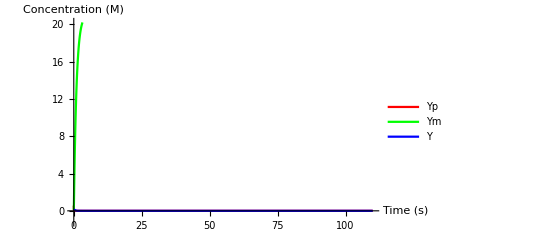

```mathematica
tmax=110;
sol=SimulateRxnsys[pCRN~Join~(conc[#,RandomReal[]]&/@SpeciesInRxnsys[pCRN]),tmax];
Plot[Evaluate[{Y[p][t],Y[m][t],Y[t]}/.sol],{t,0,tmax},PlotRange->{{0,tmax},{-1.2,20.2}},PlotStyle->{{Red},{Green},{Blue}},PlotLegends->{Yp,Ym,Y},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
Y[tmax]/.sol
```

0.000503231

```mathematica
inputConc=Module[{img=7},Flatten[{conc[Am,RandomReal[]],conc[Ap,RandomReal[]],conc[Y,RandomReal[]],conc[Zm,RandomReal[]],conc[Y[m],RandomReal[]],conc[Y[p],RandomReal[]]}~Join~Table[If[ImageVector[img][[i]]>0,
{conc[X[i,m],0],conc[X[i,p],ImageVector[img][[i]]]},
{conc[X[i,m],-ImageVector[img][[i]]],conc[X[i,p],0]}],
{i,1,Length[ImageVector[img]]}]]];
```

```mathematica
w=NaiveWeights[{2,7,12,14},Complement[Range[20],{2,7,12,14}]] (* recognize the airplane-cat-dog-toad nexus *)
```

{0.272549,0.307108,0.348775,0.366912,0.325,0.288235,0.316667,0.31201,0.270588,0.31152,0.308824,0.315931,0.275735,0.368382,0.370343,0.370343,0.332843,0.282353,0.19951,0.256373,0.341422,0.292402,0.332108,0.349755,0.282843,0.342892,0.323284,0.367402,0.329902,0.355147,0.259559,0.296078,0.387255,0.289216,0.246078,0.307843,0.189951,0.350735,0.432843,0.502941,0.343873,0.277451,0.214216,0.19951,0.272549,0.298284,0.188971,0.261029,0.329412,0.488725,0.261765,0.0973039,0.110784,0.193873,0.0838235,0.112745,0.137745,0.153431,0.235049,0.380392,0.343382,0.22402,0.304657,0.19951,-0.0115196,-0.0301471,0.00833333,0.248284,0.297549,0.359804,0.391422,0.332598,0.294608,0.269608,0.178186,0.101225,0.159314,0.263235,0.280147,0.398039,0.241667,0.259804,0.31201,0.278922,0.182843,0.136029,0.184559,0.116667,0.244608,0.413235,0.271078,0.21348,0.276716,0.315196,0.244853,0.205147,0.156618,0.131373,0.276225,0.398529}

```mathematica
pCRN=PerceptronCRN[w,-17.8];
```

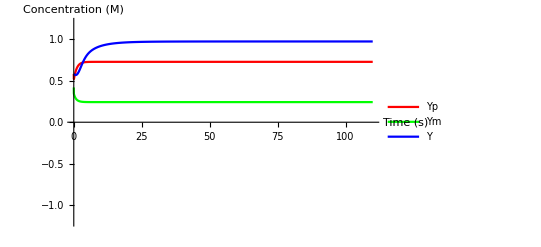

```mathematica
tmax=110;
sol=SimulateRxnsys[pCRN~Join~inputConc,tmax];
Plot[Evaluate[{Y[p][t],Y[m][t],Y[t]}/.sol],{t,0,tmax},PlotRange->{{0,tmax},{-1.2,1.2}},PlotStyle->{{Red},{Green},{Blue}},PlotLegends->{Yp,Ym,Y},
AxesLabel->{"Time (s)","Concentration (M)"}]
```

```mathematica
Y[tmax]/.sol
```

0.992403

We can see that the CRN correctly classifies the training examples. I think that the bias is really interesting part of the system to me. Right now we have to manually tune because we aren’t doing any training, but I think it would be interesting to create a CRN that trains a perception or another type of model.